1)

```mathematica
Clear[aminus];
aminus:=(x#+I(-I D[#,x]))/Sqrt[2]&;
Clear[aplus];
aplus:=(x #-I(-I D[#,x]))/Sqrt[2]&;
```

2 - 3)

```mathematica
psi0 = psi0[x] /. DSolve[aminus[psi0[x]]==0,psi0[x],x];
psi0n = Flatten[psi0 /.Solve[Integrate[(Abs[psi0])^2,{x,-∞,∞}] == 1,C[1]]] // First;
?psi0n
```

Global`psi0n

psi0n=-(ⅇ^(-x^2/2))/π^(1/4)

4 - 5)

```mathematica
Clear[psi];
psi[0]=psi0n;
psi[n_]:=psi[n]=aplus[psi[n-1]]/Sqrt[n];
arrpsi=Table[Simplify[psi[n]],{n,0,5}]
```

{-(ⅇ^(-x^2/2))/π^(1/4),-(√2 ⅇ^(-x^2/2) x)/π^(1/4),(ⅇ^(-x^2/2) (1-2 x^2))/(√2 π^(1/4)),(ⅇ^(-x^2/2) (3 x-2 x^3))/(√3 π^(1/4)),-(ⅇ^(-x^2/2) (3-12 x^2+4 x^4))/(2 √6 π^(1/4)),-(ⅇ^(-x^2/2) x (15-20 x^2+4 x^4))/(2 √15 π^(1/4))}

6)

```mathematica
Integrate[arrpsi^2,{x,-∞,∞}]
```

{1,1,1,1,1,1}

7 - 8)

```mathematica
Clear[h];
h:=aplus@aminus@#+1/2#&;
Attributes[h]={Listable};
Factor[h[arrpsi]/arrpsi]
```

{1/2,3/2,5/2,7/2,9/2,11/2}

9)

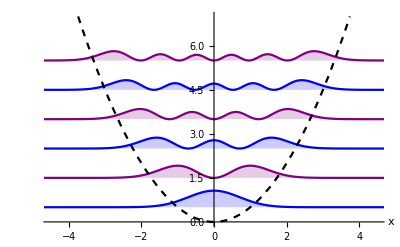

```mathematica
Plot[{Evaluate[arrpsi^2+Factor[h[arrpsi]/arrpsi]],1/2 x^2},{x,-5,5},PlotRange->{{-4.5,4.5},{0,7}},PlotStyle->{Blue,Purple,Blue,Purple,Blue,Purple,Directive[Dashed,Black]},Filling-> {1->1/2,2->3/2,3->5/2,4->7/2,5->9/2,6->11/2},AxesLabel->{x}]
(*как вы легенду нарисовали на самих линиях? Не смог найти*)
```

10)

```mathematica
Clear[matrixElement];
matrixElement[f_,n1_,n2_]:=Integrate[psi[n1]f[psi[n2]],{x,-∞,∞}];
f1=h;
f2=-I D[#,x]&;
f3=x#&;
f4 = aplus;
matrixElement[f1,1,1]
matrixElement[f1,2,1]
matrixElement[f2,2,3]
matrixElement[f3,4,3]
matrixElement[f4,0,0]
matrixElement[f4,2,1]
```

3/2

0

-ⅈ √(3/2)

√2

0

√2